```mathematica
data=Import["C:\\Users\\Evan\\GitProjects\\weather-prediction\\data2\\fullTest\\identity.csv"];
HIDDEN = 1;
DISTANCE = 2;
LEARNING  = 3;
ITERATIONS = 4;
TIME = 5;
EWXSTD = 6;
GRKSTD = 7;
data1=Select[data,#[[DISTANCE]]==1&];
data2=Select[data,#[[DISTANCE]]==1.5&];
```

```mathematica
Table[
Select[
data1[[All,{HIDDEN,ITERATIONS,EWXSTD}]],
#[[1]]==HID&
][[All,{2,3}]],
{HID,{0,1,2,4,8}}]
```

{{{1,0.33254},{2,0.220315},{4,0.152645},{8,0.106598},{16,0.0746612}},{{1,0.417135},{2,0.276152},{4,0.166789},{8,0.117833},{16,0.0702406}},{{1,0.416407},{2,0.293144},{4,0.200202},{8,0.130094},{16,0.0784018}},{{1,0.43031},{2,0.280796},{4,0.202562},{8,0.126316},{16,0.0952394}},{{1,0.419948},{2,0.293707},{4,0.191714},{8,0.142639},{16,0.0845566}}}

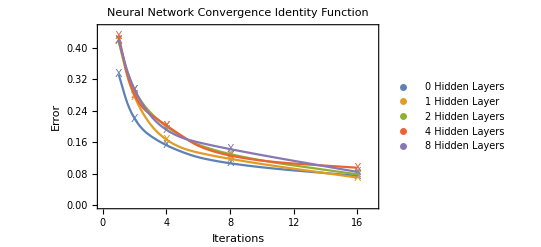

```mathematica
Show[ListPlot[
Table[
Select[
data1[[All,{HIDDEN,ITERATIONS,EWXSTD}]],
#[[1]]==HID&
][[All,{2,3}]],
{HID,{0,1,2,4,8}}],
PlotStyle->Directive[FontSize->14],
PlotLegends->{"0 Hidden Layers","1 Hidden Layer","2 Hidden Layers", "4 Hidden Layers", "8 Hidden Layers"},
PlotMarkers->"X"],
ListLinePlot[
Table[
Select[
data1[[All,{HIDDEN,ITERATIONS,EWXSTD}]],
#[[1]]==HID&
][[All,{2,3}]],
{HID,{0,1,2,4,8}}],
InterpolationOrder->2]
,FrameLabel->{ Style["Iterations",FontSize->18], Style["Error",FontSize->18]},
Frame->True,
PlotLabel->Style["Neural Network Convergence\nIdentity Function",FontSize->20],
PlotRange->{{0,17},{0,0.45}}]
```

```mathematica
Export["C:\\Users\\Evan\\Dropbox\\Grad_School\\legend.png",]
```

C:\Users\Evan\Dropbox\Grad_School\legend.png

```mathematica
Show[ListPointPlot3D[
data1[[All,{HIDDEN,ITERATIONS,TIME}]],PlotStyle->Directive[PointSize[0.02],Blue]],
ListPointPlot3D[
data2[[All,{HIDDEN,ITERATIONS,TIME}]],PlotStyle->Directive[PointSize[0.02],Red]]
,AxesLabel->{"HIDDEN", "ITER", "TIME"},
PlotRange->{{0,8},{0,20},{0,2000000}}]
```

-Graphics3D-

```mathematica
Manipulate[LinearModelFit[Select[Select[data,#[[DISTANCE]]==DIST&],#[[HIDDEN]]==HID&][[All,{ITERATIONS,TIME}]],{iter},{iter}],{DIST,{1,1.5}},{HID,{0,1,2,4,8}}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data, #1 ⟦ DISTANCE ⟧ == FE`DIST$$15 &].

Part::pkspec1: The expression HIDDEN cannot be used as a part specification.

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

Part::pkspec1: The expression {ITERATIONS, TIME} cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.